```mathematica
pauliMatrix[0]={{1,0},{0,1}};
pauliMatrix[1]={{0,1},{1,0}};
pauliMatrix[2]={{0,-ⅈ},{ⅈ,0}};
pauliMatrix[3]={{1,0},{0,-1}};

(*Definition of the matrices ψ*)
DiracMatrix[i_Integer?Positive,Dimension->n_Integer?Positive]/;If[OddQ[n],n=!=i,True]:=Module[{ν=n/2},Which[i==1,KroneckerProduct@@Table[pauliMatrix[1],{ν}],

2 ν>i>1&&EvenQ[i],
KroneckerProduct[Sequence@@Table[pauliMatrix[1],{ν-i/2}],pauliMatrix[2],Sequence@@Table[pauliMatrix[0],{i/2-1}]],2 ν>i>1&&OddQ[i],KroneckerProduct[Sequence@@Table[pauliMatrix[1],{ν-(i-1)/2}],pauliMatrix[3],Sequence@@Table[pauliMatrix[0],{(i-1)/2-1}]],
i==2 ν,KroneckerProduct[pauliMatrix[2],Sequence@@Table[pauliMatrix[0],{ν-1}]]]]

DiracMatrix[i_Integer?Positive,Dimension->n_Integer?Positive]/;n==i&&OddQ[i]:=Module[{ν=(n-1)/2},(-I)^ν Dot@@Table[DiracMatrix[j,Dimension->n],{j,2ν}]]
```

```mathematica
(* We need to have 1 << βJ << N. Here we have βJ=5 and N=14... *)
(* We also need to have q << N. Here we have q=2 and N=14... *)
n=14; (* The number of fermions in our system *)
q=2; (* The interactions in our system *)
s=((q-1)!)/n^(q-1)J^2;
J=1;
dist= 1/(√(2π s))ⅇ^(-x^2/(2s)); 
gauss=ProbabilityDistribution[dist,{x,-Infinity, Infinity}];
random := RandomVariate[gauss];
```

```mathematica
iteration:=Module[{},
(*Generating the random coupling tensor Subscript[J, abcd]*)
tensorJ = Normal@ SymmetrizedArray[_ :> random, {n,n},Antisymmetric[All]];
(*Generates an array containing all Subscript[ψ, i] from i=1 to n*)
psi= Table[DiracMatrix[i,Dimension-> n],{i,n}]; 
(*Definition of the Hamiltonian*)
H=Sum[If[a<b , ⅈ^(q/2)*tensorJ[[a,b]]*psi[[a]].psi[[b]],0],{a,n},{b,n}];
evalH = Eigenvalues[H];
diagH = DiagonalMatrix[evalH];
Zt = Sum[ⅇ^(-(β+I*t)evalH[[i]]),{i,2^Floor[n/2]}];
Z= Sum[ⅇ^(-β*evalH[[i]]),{i,2^Floor[n/2]}];
{Zt,Z}]
```

```mathematica
time=Timing[samples=1000;
β=5;
Zfuncs=Table[iteration,samples];avgZts = Sum[Zfuncs[[i,1]]*Conjugate[Zfuncs[[i,1]]],{i,samples}]/samples;
avgZ= Sum[Zfuncs[[i,2]],{i,samples}]/samples;
gt=avgZts/(avgZ)^2;];
time[[1]]
```

12674.4

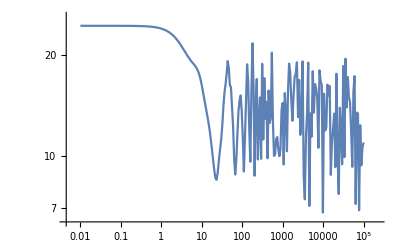

```mathematica
LogLogPlot[gt,{t,0.01,10^5},PlotPoints->5]
```